# Determination of α, β by fitting σ_R to ϵ at Q^2= 3.25 (GeV)^2

R^2/τ =A

2/R= B

2R/τ= X

R/τ= L

(G_M)^2 = G

σ_R = (G_M)^2 [1 + ϵ A + (B + ϵ X)[α1 (ϵ - 1) + α2 (ϵ^2 - 1)] + [B {1 -( 2 R ϵ/(1 + ϵ))} + 2 ϵ (1 + D)] [β1 (ϵ - 1) + β2 (ϵ^2 - 1)] ]

## Qattan

```mathematica
epsdata={0.426,0.609,0.719,0.865}; 
sigmaRdata={0.008395241,0.008614507,0.008723768,0.008757643};
data=Transpose[{epsdata,sigmaRdata}]
A=0.052938019
B=9.0455985
X=0.478856064
L=0.239428032
G=0.016023135
R=0.221102009

sigmaR=G*(1+(eps*A)+((B+(eps*X))*(alpha1*(eps-1)+alpha2*(eps^2-1)))+(B*(1-((eps*2*R)/(1+eps)))+ 2*eps*(1+L))*(beta1*(eps-1)+beta2*(eps^2-1)))

FindFit[data, {sigmaR},{alpha1,alpha2,beta1,beta2},eps]
```

{{0.426,0.00839524},{0.609,0.00861451},{0.719,0.00872377},{0.865,0.00875764}}

0.052938

9.0456

0.478856

0.239428

0.0160231

0.221102

0.0160231 (1+0.052938 eps+(9.0456+0.478856 eps) (alpha1 (-1+eps)+alpha2 (-1+eps^2))+(beta1 (-1+eps)+beta2 (-1+eps^2)) (2.47886 eps+9.0456 (1-(0.442204 eps)/(1+eps))))

{alpha1→106.502,alpha2→-56.8885,beta1→-111.508,beta2→59.7824}

## Y_E and Y_ 3 Determination with Plot

### α values :

```mathematica
alpha1=106.50196943748504
alpha2=-56.88847673999647
alpha0=-(alpha1+alpha2)
```

106.502

-56.8885

-49.6135

### β values :

```mathematica
beta1=-111.50835480162051
beta2=59.782371191251976
beta0=-(beta1+beta2)
```

-111.508

59.7824

51.726

### Y_E , Y_ 3 & Y_M :

-49.6135+106.502 eps-56.8885 eps^2

51.726-111.508 eps+59.7824 eps^2

4.5228 (-49.6135+106.502 eps-56.8885 eps^2+(51.726-111.508 eps+59.7824 eps^2) (1-(0.442204 eps)/(1+eps)))

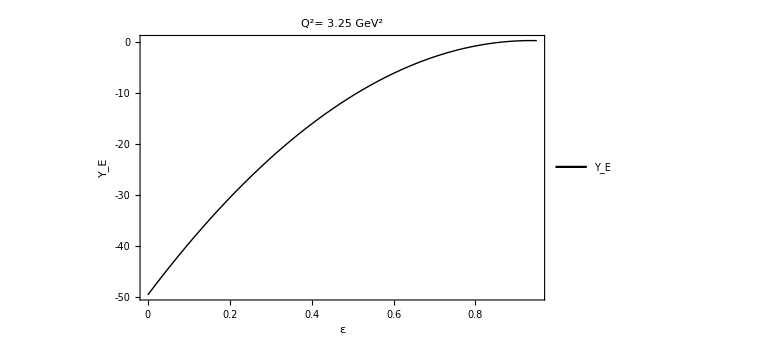

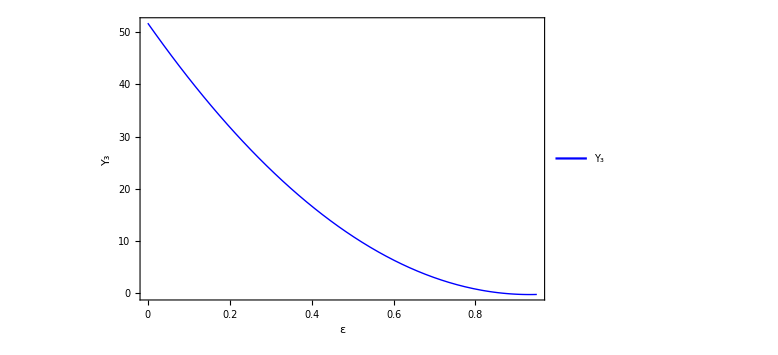

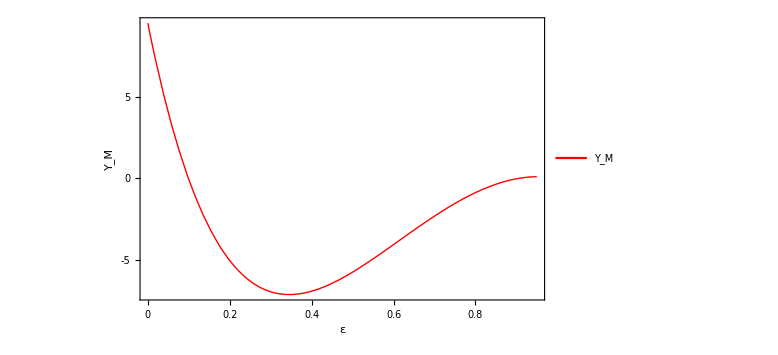

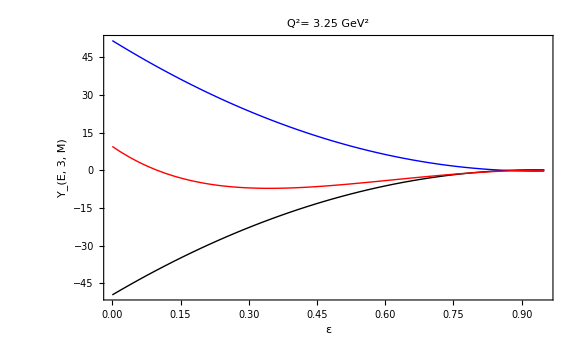

```mathematica
YE=-49.613492697488574+(106.50196943748504*eps)+(-56.88847673999647*eps^2)
Y3=51.72598361036854+(-111.50835480162051*eps)+(59.782371191251976*eps^2)
YM=(YE+(1-R*(2*eps/(1+eps)))*Y3)/R
YEplot=Plot[YE, {eps,0,0.95},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.92,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 3.25 GeV^2",Bold,24], ImageSize-> Large]
Y3plot=Plot[Y3, {eps,0,0.95},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplot=Plot[YM, {eps,0,0.95},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplot,Y3plot,YMplot, PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,12],ImageSize->Large]
```

## My Fit

```mathematica
Q2=3.25
fcmuR=1+(-0.11723721716472688)*Q2+(0.0025226146422440594)*(Q2)^2+(-0.0004347472619650877)*(Q2)^3
fcR=fcmuR/2.7972
```

3.25

0.6307

0.225476

```mathematica
epsdata={0.426,0.609,0.719,0.865}; 
sigmaRdata={0.008395241,0.008614507,0.008723768,0.008757643};
data=Transpose[{epsdata,sigmaRdata}]
Afc=0.055337504
Bfc=8.84731251
Xfc=0.48959
Lfc=0.24479
Gfc=0.015986704
Rfc=0.2254755123055896

sigmaRfc=Gfc*(1+(eps*Afc) +((Bfc+(eps*Xfc))*(alpha1fc*(eps-1)+alpha2fc*(eps^2-1)))+(Bfc*(1-((eps*2*Rfc)/(1+eps)))+ 2*eps*(1+Lfc))*(beta1fc*(eps-1)+beta2fc*(eps^2-1)))
FindFit[data, {sigmaRfc},{alpha1fc,alpha2fc,beta1fc,beta2fc},eps]
```

{{0.426,0.00839524},{0.609,0.00861451},{0.719,0.00872377},{0.865,0.00875764}}

0.0553375

8.84731

0.48959

0.24479

0.0159867

0.225476

0.0159867 (1+0.0553375 eps+(8.84731+0.48959 eps) (alpha1fc (-1+eps)+alpha2fc (-1+eps^2))+(beta1fc (-1+eps)+beta2fc (-1+eps^2)) (2.48958 eps+8.84731 (1-(0.450951 eps)/(1+eps))))

{alpha1fc→106.926,alpha2fc→-56.9295,beta1fc→-112.051,beta2fc→59.8889}

```mathematica
alpha1fc=106.92641663313402
alpha2fc=-56.92947388288125
alpha0fc=-(alpha1fc+alpha2fc)
beta1fc=-112.05086820821832
beta2fc=59.88890984563869
beta0fc=-(beta1fc+beta2fc)
```

106.926

-56.9295

-49.9969

-112.051

59.8889

52.162

```mathematica
YEfc=alpha0fc+(alpha1fc*eps)+(alpha2fc*eps^2)
Y3fc=beta0fc+(beta1fc*eps)+(beta2fc*eps^2)
YMfc=(YEfc+(1-Rfc*(2*eps/(1+eps)))*Y3fc)/Rfc
```

-49.9969+106.926 eps-56.9295 eps^2

52.162-112.051 eps+59.8889 eps^2

4.43507 (-49.9969+106.926 eps-56.9295 eps^2+(52.162-112.051 eps+59.8889 eps^2) (1-(0.450951 eps)/(1+eps)))

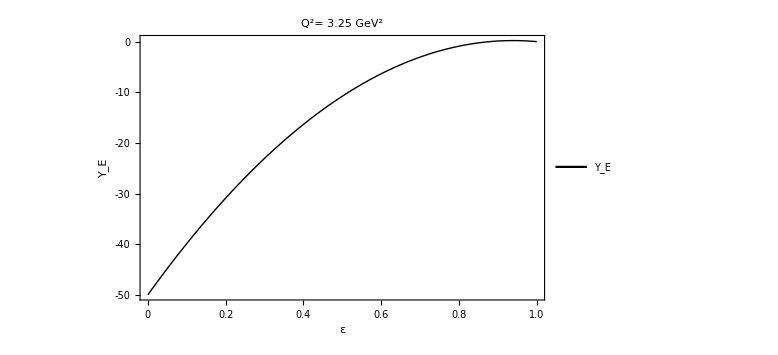

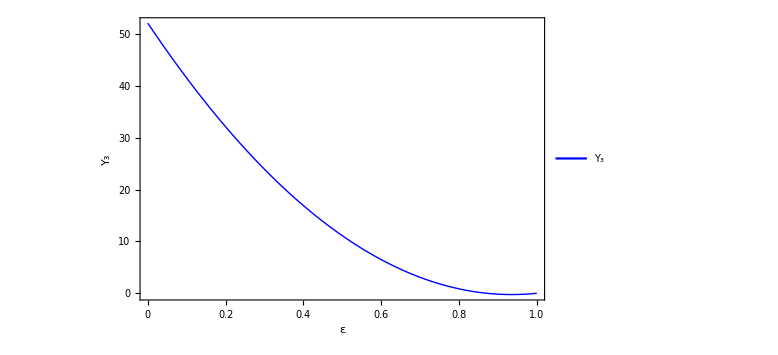

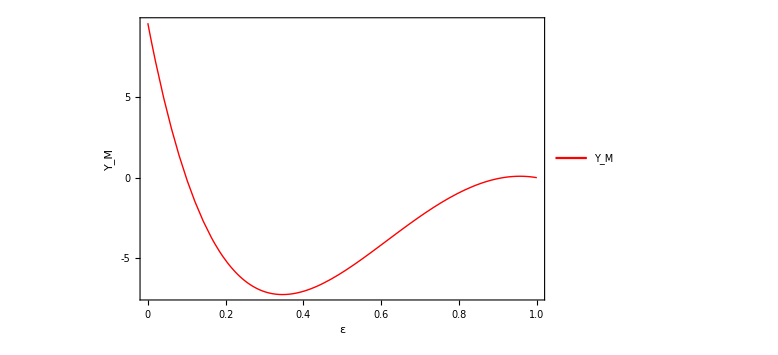

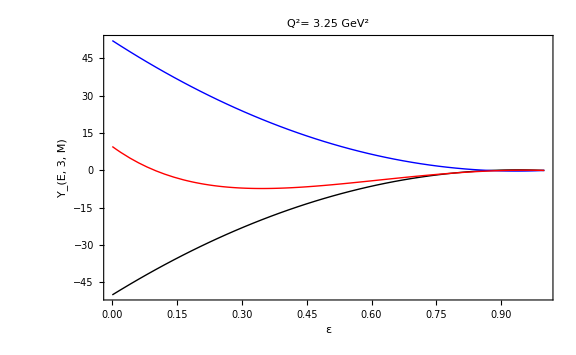

```mathematica
YEplotfc=Plot[YEfc, {eps,0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.9,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 3.25 GeV^2",Bold,24], ImageSize-> Large]
Y3plotfc=Plot[Y3fc, {eps,0,1},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplotfc=Plot[YMfc, {eps,0,1},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplotfc,Y3plotfc,YMplotfc,PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,14],ImageSize-> Large]
```